# Analyzing Economic Trends: A Comparative Study of State-Space Models and Neural Networks

Muhammad Ali Hafeez

Abstract

## Introduction

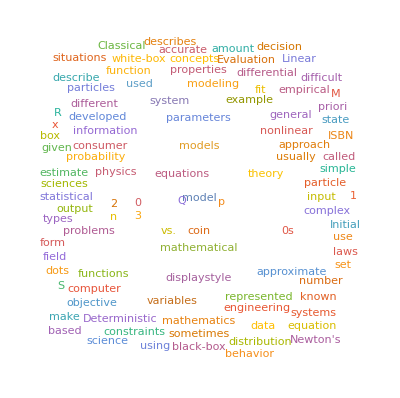

```mathematica
WordCloud[WikipediaData["Mathematical Modeling"]]
```

The purpose of this essay is to introduce a highly significant discussion. The emergence of machine learning has brought about groundbreaking advancements. However, have we thoroughly analyzed each technique in terms of their predictive power relative to one another? This essay aims to compare two crucial techniques: State-Space Models, specifically those employing the Kalman filter, and Neural Networks, which represent a more contemporary approach.

## Data

The data that will be used in this computational essay is the Federal Reserve of Economic Data (FRED) Real Gross Domestic Product data from 1947 to 2023.

```mathematica
data=Import["C:\\Users\\ali12\\Downloads\\GDP.xls"];
preprocessedData=data/. Null->""; 
splitData=Partition[Flatten[preprocessedData],2];
table=Grid[splitData,Alignment->Center]//DisplayForm;
styledTable=StyleBox[table,GridBoxOptions->{GridBoxDividers->{"Columns"->True},GridBoxItemStyle->{"ColumnBands"->{{1,1}->Bold},"Columns"->{2->Bold}}}];
scrollableTable=Pane[styledTable,ImageSize->{Automatic,300},Scrollbars->True];
scrollableTable
```

## Splitting the Data into Train and Test Sets

In this context, we will employ Mathematica to partition the dataset into separate testing and training sets. This division serves the purpose of evaluating the predictive capabilities of our models and safeguarding against the occurrence of overfitting.

```mathematica
whole=preprocessedData;
{tester,trainer}=ResourceFunction["TrainTestSplit"][(#1->#2)&@@#&/@Drop[#&@@whole,11],Shuffle->False];
tester
trainer
```

## Using A Non-linear Model Fit

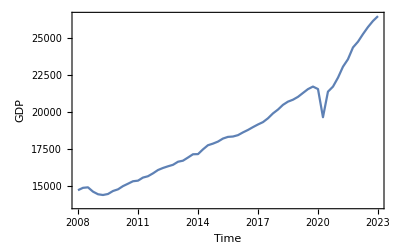

FittedModel[ax+«3»+0.128037 (0.128037 («7»+(T…0«1»→«10»))+«59»+«18» («1»))]

```mathematica
whole1=preprocessedData;
{tester1,trainer1}=ResourceFunction["TrainTestSplit"][(#1->#2)&@@#&/@Drop[#&@@whole1,11],Shuffle->False];
DateListPlot[TimeSeries[trainer1],FrameLabel->{"Time","GDP"}]
Clear[x]
model=ax+bx^2+cx^3+gx^4+e;
nlm=NonlinearModelFit[trainer1,model,{a,b,c,g,e},x]
```

## Using State Space Modeling

```mathematica
whole2=preprocessedData;
{tester2,trainer2}=ResourceFunction["TrainTestSplit"][(#1->#2)&@@#&/@Drop[#&@@whole2,11],Shuffle->False];
DateListPlot[TimeSeries[trainer2],FrameLabel->{"Time","GDP"}]
ts=TimeSeries[trainer2];
resampledTS=TimeSeriesResample[ts]
ts=TimeSeriesModelFit[resampledTS]
```

## Using Neural Networks